```mathematica
Nt = 551 ;(*151*)
ti = 0; tf =1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = 0; xf = 2*Pi;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.159155

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];

f[x_] = ⅇ^(- 8(x-π)^2);
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
(*CN*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
UCN = Chop[UCN, 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]

UCNold= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCNold[[1,All]] = N[f[X],32];
UCNold = N[UCNold,32];
UCNold = Chop[UCNold, 10^(-307)];
UCNold = Developer`ToPackedArray[UCNold, Real]; 
Developer`PackedArrayQ[UCNold]


I1 = N[IdentityMatrix[Length[D1]],32];
A = N[I1 - ((DL / 2)),32];
B = N[I1 + ((DL / 2)),32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = Developer`ToPackedArray[EMCN, Real]; 

Do[UCNold[[n+1,All]] = UCNold[[n,All]] + (EMCN).UCNold[[n,All]], {n,1,Nt - 1 }];

yerr = 0;
Do[
Do[
delta = Total[(EMCN[[m,All]]) * UCN[[n,All]]] + yerr;
UCN[[n+1,m]] = UCN[[n,m]] +  delta;
yerr = (UCN[[n,m]] - UCN[[n+1,m]]) + delta

,{m,1,Length[EMCN]}]
,{n,1,Nt - 1}]
```

True

True

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
FCN = Developer`ToPackedArray[FCN, Real];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
intCN = Developer`ToPackedArray[intCN, Real];

FCNold = Table[0,{i,1,Nt},{j,1,Nx}];
FCNold = Developer`ToPackedArray[FCNold, Real];
intCNold = Table[0,{i,1,Length[FCNold[[All,1]]]}];
intCNold = Developer`ToPackedArray[intCNold, Real];
Do[
FCN[[i]] = (D1.UCN[[i,All]])^2;

intCN[[i]] = (2π)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];

Do[
FCNold[[i]] = (D1.UCNold[[i,All]])^2;

intCNold[[i]] = (2π)/Nx Total[FCNold[[i,All]]]
,{i,1,Length[FCNold[[All,1]]]}];
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
energyErrorLD2old = Abs[intCNold - intCNold[[1]]];
```

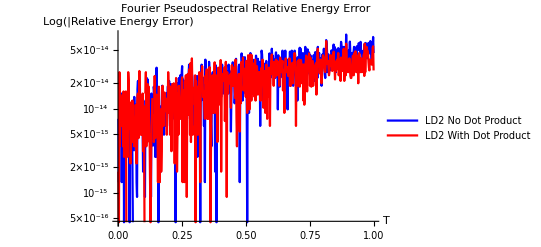

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}],Transpose[{T,energyErrorLD2old}]},PlotStyle->{Blue,Red},PlotLegends->{"LD2 No Dot Product", "LD2 With Dot Product"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Fourier Pseudospectral Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorLD2]}},Joined->True]
```

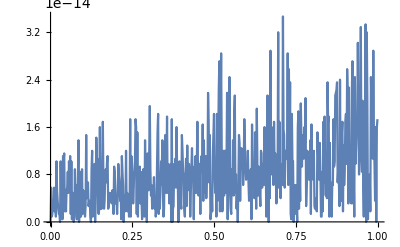

```mathematica
ListLinePlot[Transpose[{T,Abs[energyErrorLD2 - energyErrorLD2old]}],PlotRange->All]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
fexact[t_,x_] = ⅇ^(- 8((x-t)-π)^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
```

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)

abserrLD2old = Abs[UCNold-Uexact];
errorLD2old = Table[0,{i,1,Length[abserrLD2old]}];
errorLD2old = Developer`ToPackedArray[errorLD2old, Real];
Do[
errorLD2old[[i]] = Norm[abserrLD2old[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2old]}
];
```

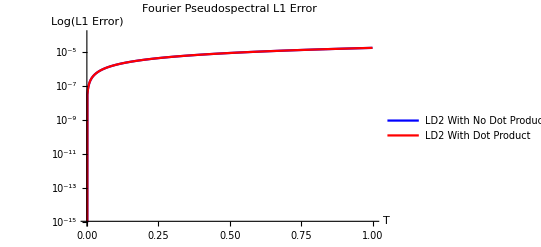

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}],Transpose[{T,errorLD2old}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-4}}, PlotStyle->{Blue, Red},PlotLegends->{"LD2 With No Dot Product", "LD2 With Dot Product"},Axes -> True, AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

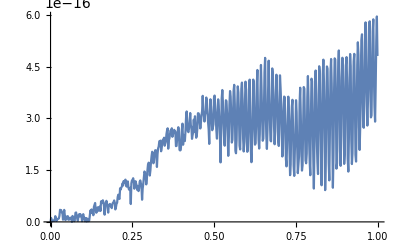

```mathematica
ListLinePlot[Transpose[{T,Abs[errorLD2 - errorLD2old]}],PlotRange->All]
```